```mathematica
KcpuO1=Import["Tests.xlsx",{"Data",1,{5,6,7,8,9},2}];
KgpuO1=Import["Tests.xlsx",{"Data",1,{5,6,7,8,9},3}];

RcpuO1=Import["Tests.xlsx",{"Data",1,{5,6,7,8,9},4}];
RgpuO1=Import["Tests.xlsx",{"Data",1,{5,6,7,8,9},5}];
```

```mathematica
KcpuO2=Import["Tests.xlsx",{"Data",1,{14,15,16,17,18},2}];
KgpuO2=Import["Tests.xlsx",{"Data",1,{14,15,16,17,18},3}];

RcpuO2=Import["Tests.xlsx",{"Data",1,{14,15,16,17,18},4}];
RgpuO2=Import["Tests.xlsx",{"Data",1,{14,15,16,17,18},5}];
```

```mathematica
KcpuO3=Import["Tests.xlsx",{"Data",1,{23,24,25,26},2}];
KgpuO3=Import["Tests.xlsx",{"Data",1,{23,24,25,26},3}];

RcpuO3=Import["Tests.xlsx",{"Data",1,{23,24,25,26},4}];
RgpuO3=Import["Tests.xlsx",{"Data",1,{23,24,25,26},5}];
```

```mathematica
ndof1=Import["Tests.xlsx",{"Data",1,{31,32,33,34,35},3}];
ndof2=Import["Tests.xlsx",{"Data",1,{31,32,33,34,35},4}];
ndof3=Import["Tests.xlsx",{"Data",1,{31,32,33,34},5}];
```

```mathematica
KCPU1=Thread[{ndof1,KcpuO1}];
KCPU2=Thread[{ndof2,KcpuO2}];
KCPU3=Thread[{ndof3,KcpuO3}];

RCPU1=Thread[{ndof1,RcpuO1}];
RCPU2=Thread[{ndof2,RcpuO2}];
RCPU3=Thread[{ndof3,RcpuO3}];

KGPU1=Thread[{ndof1,KgpuO1}];
KGPU2=Thread[{ndof2,KgpuO2}];
KGPU3=Thread[{ndof3,KgpuO3}];

RGPU1=Thread[{ndof1,RgpuO1}];
RGPU2=Thread[{ndof2,RgpuO2}];
RGPU3=Thread[{ndof3,RgpuO3}];
```

```mathematica
PlotTemplate[Data_,Legend_,xlabel_,ylabel_]:=
ListLogLogPlot[Data,GridLines->Automatic, GridLinesStyle->Directive[Gray, Dashed], Frame->True,Joined->True,PlotMarkers->Automatic,FrameLabel->{xlabel,ylabel},PlotLegends->LineLegend[Legend,LegendFunction->(Framed[#,RoundingRadius->2.75]&),LegendMargins->1],LabelStyle->Directive[Black,FontSize->14,Frame->True],PlotStyle->ColorData[81,"ColorList"]];
```

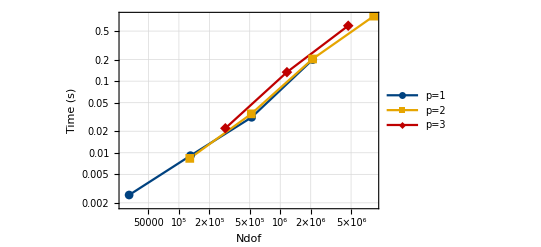

```mathematica
data={KCPU1, KCPU2,KCPU3};
legend={"p=1","p=2","p=3"};
x="Ndof";
y="Time (s)";
PlotTemplate[data,legend,x,y]
```